```mathematica
coefs={0.6549346562166292,0.0007360327863181,1.7208438040910521,0.0093172365407013,-2.3017475785155712,-0.4862872792352397,0.5431782452937021,0.2936652309426779,-0.0012534629722414,-0.0012792106699577,-0.0034638170256471,0.0022907416729538,-0.0002068271494215,-0.0064494439848317,-0.0037325914743524,-0.0004503931641482};
```

```mathematica
F[x_]:=1+x^2
min=-1
max=1
```

-1

1

```mathematica
FourierApprox[coefs_][x_]:=Sum[coefs[[i+1]]*Sin[i*x], {i, 0,Length[coefs]-1}]
TaylorApprox[coefs_][x_]:=Sum[coefs[[i+1]]*x^i/Factorial[i], {i, 0, Length[coefs]-1}]
IntegralLoss[f_]:=NIntegrate[(F[x]-f[f[x]])^2, {x, min, max}]
```

```mathematica
approx=TaylorApprox[coefs];
```

```mathematica
IntegralLoss[approx]
```

0.0000408767

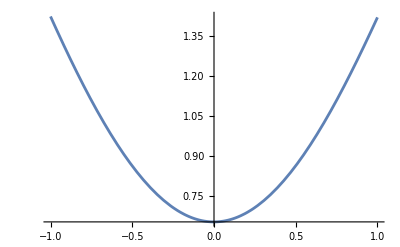

```mathematica
Plot[ approx[x], {x, min, max}]
```

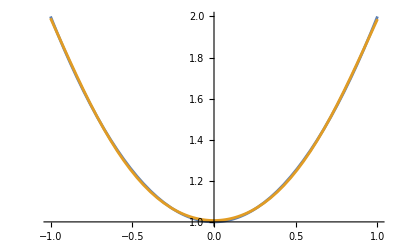

```mathematica
Plot[{F[x], approx[approx[x]]}, {x, min, max}]
```

```mathematica
approx[x]
```

0.654935+0.000736033 x+0.860422 x^2+0.00155287 x^3-0.0959061 x^4-0.00405239 x^5+0.000754414 x^6+0.0000582669 x^7-3.10879×10^-8 x^8-3.52516×10^-9 x^9-9.54535×10^-10 x^10+5.73879×10^-11 x^11-4.31788×10^-13 x^12-1.03572×10^-12 x^13-4.28156×10^-14 x^14-3.44423×10^-16 x^15

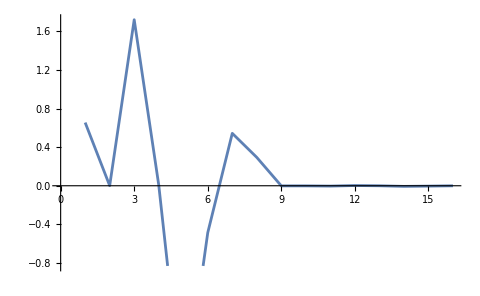

```mathematica
ListLinePlot[coefs]
```